# Kerr modified optomechanics - scattering response calculation (S_21)

This notebook gives us the numerical solution of the scattering response of the cavity in the given electromechanical system. The electromechanical device is given by the standard optomechanical Hamiltonian with the addition of a Kerr non-linearity in the cavity mode. The equations of motion are used from the paper  “Self-sustained Oscillations of a Non-linear Optomechanical System in the Low Excitation Regime”.

```mathematica
ClearAll["Global`*"] (*Clears all previously defined variables*)
```

### System parameters - Here we will define all the system parameters.

```mathematica
ωm=2*Pi*5.607483*10^6; (*Mechanical frequency (will be used to normalise all other varaibles)*)

γ=(2*Pi*11.7)/(2*Pi*5.606456*10^6); (*Mechanical damping rate normlised with respect to mechanical frequency Subscript[ω, m]*)

 Ω=(2*Pi*5.607483*10^6)/(2*Pi*5.607483*10^6); (*Normalised mechanical frequency ~ Ω=1 *)

κe=(2*Pi*1.636293*10^6)/(2*Pi*5.607483*10^6); (*Cavity decay rate associated with external losses normalised with respect to Subscript[ω, m]*)

κint=(2*Pi*0.675812*10^6)/(2*Pi*5.607483*10^6);(*Internal cavity decay rate normalised with respect to Subscript[ω, m]*)

κ=κe+κint; (*Total cavity decay rate given by sum of external and internal decay rate.*)

g0=(2*Pi*4.691*10^3)/(2*Pi*5.607483*10^6); (*Optomechanical coupling strength normalised with Subscript[ω, m]*)

Kerr=(2*Pi*0.07*10^6)/(2*Pi*5.607483*10^6); (*Kerr non-linearity associated with the cavity mode normalised with respect to mechanical frequency Subscript[ω, m] *)

Kerreff=Kerr+(2 g0^2 Ω)/(Ω^2+γ^2/4);
(*Effective Kerr non-linearity given by the sum of cavity kerr and the nonlinearity associated with the optomechanical interaction. *)

nincrit=2*κ^3/(3 Sqrt[3] κe Kerreff);(*Critical input power Subscript[n, crit] which is the input power at which the system becomes bistable. Since we have a non-zero Kerr non-linearity, beyond Subscript[n, crit] the system enters a regime with three possible solutions for the photon number. It is qualitatively similar to the three photon branches of a Kerr resonator.*)

time=0.8*ωm;(*Time of simulation which is multiplied with mechanical frequency because the system parameters are all normalised with mechanical frequency. The time is chosen such that the system reaches steady state for the given set of system parameters.*)
```

### Define a scattering response function

```mathematica
(*~~~~~~Define function scattable~~~~~~*)
scattable[δ_,nin_]:=
(* ~~~Equations of motion ~~~*)
(*Define the equations of motion for Subscript[α, r],Subscript[α, i],Subscript[β, r],Subscript[β, i]. Here Subscript[α, r](Subscript[β, r]) and Subscript[α, i](Subscript[β, i]) are the real and imaginary part of the cavity (mechanical) mode respectively. In addition to the equations of motion, we also define the initial conditions for all the variables. For this work, we always assume that the system starts with zero photon/phonon occupation, therefore Subscript[α, r][0]=Subscript[α, i][0]=Subscript[β, r][0]=Subscript[β, i][0]=0. *)(eqns6={αR'[t]==-δ αI[t] - κ/2 αR[t] - Kerr ((αR[t])^2+(αI[t])^2) αI[t] + 2 g0 βR[t] αI[t] - Sqrt[κe/2] Sqrt[nin], αI'[t]==δ αR[t] - κ/2 αI[t] + Kerr ((αR[t])^2+(αI[t])^2) αR[t]-2 g0 βR[t] αR[t], βR'[t]==Ω βI[t] - γ/2 βR[t], βI'[t]==-Ω βR[t] - γ/2 βI[t] -  g0 ((αR[t])^2+(αI[t])^2) ,αR[0]==0.0,αI[0]==0.0,βR[0]==0.0,βI[0]==0.0};

sol6va=NDSolveValue[eqns6,{αR,αI,βR,βI},{t,0,time},Method->"StiffnessSwitching"];(* Obtain the solution for the equations of motion for a given amount of time.*)

tab=Table[Abs[(Sqrt[nin]+Sqrt[κe/2]*(sol6va[[1]][t]+I*sol6va[[2]][t]))/(Sqrt[nin])],{t,0.999*time,time}]; (*Table to store the Subscript[S, 21] values for different values of time. The time is chosen so that the system has already reached steady state. The response is calculated using the standard input-output relation, details of which can be found in the Appendix of the paper.*)

scatoutval=Mean[tab](*Time average of Subscript[S, 21]. The experiment measures the scattering response as a function of time and averages the response after the system has reached steady state. Therefore we obtain a time average of the scattering response in the steady state regime.*))
(*~~~~~End of function~~~~~~~~~*)
```

### Calling the scattering response function

S21-sample-data.csv

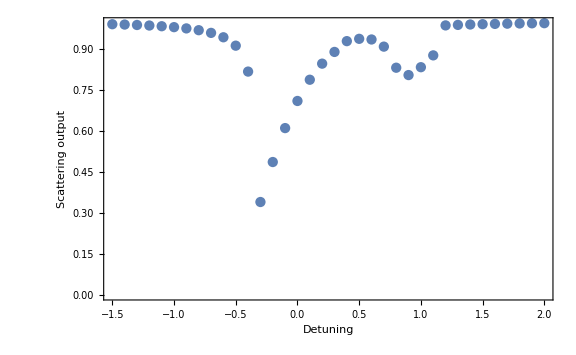

```mathematica
scatsim=Table[{i,scattable[i,1.10*nincrit]},{i,-1.5,2,0.1}];

Export["S21-sample-data.csv",scatsim] (*To export the generated table in the form of a CSV file*)

(*Plot the scattering response as a function of detuning/frequency. *)
ListPlot[scatsim,PlotRange->All,BaseStyle->{FontSize->16,FontFamily->"Times New Roman"},Frame->True,LabelStyle->Directive[FontSize->16],ImageSize->Large,FrameTicksStyle->Directive[Black,20,Thin],FrameLabel->{"Detuning","Scattering output"}]
```

### End of notebook

Note : - This is a sample code to obtain the S_21response as a function of detuning for a fixed input power. To generate figures for different input powers, modify “1.10*nincrit” to the specific power. 
Additionally, the system parameters can be changed to obtain the response for different values of optomechanical coupling and Kerr non-linearity.  Currently the parameters shown here correspond to Figure 4 (III b) in the paper. Note that the simulations take a long time, since the experimental setup requires around 1 s to reach steady state. For this sample code, we chose the bin size to be 0.1, however for generating all the plots in the paper, we have used a bin size of 0.025.